# Atomic ADM Cooling Rates - Notebook

Behold, the horror of running one of my Mathematica notebooks. I apologise in advance.

```mathematica
Clear["Global`*"]
```

```mathematica
k=1.38*^-23;
c=299792458;
h=6.63*^-34;
α=1/137;
me = 5.11*^-4; (*GeV*)
mp = 0.93827; 
GeVtograms=1.783*10^-24;
gramstoMsol = 5.03*10^-34; 
cmtokpc = 3.241*10^-22;

Mdwarf = 10^10; (*Msun*)
Gnewton =4.3*^-9 ; (*Mpc(km/s)^2/Msun*)
Gnewtonkpc = Gnewton*10^3; (*kpc (km/s)^2/Msun*)
kb = 1.381*^-16; (*ergs/Kelvin*)
GeVtoMsun = 8.97*^-58;
secondstoGYr = 3.171*^-17;
kpctocm = 3.086*^21;
kmtoMpc = 3.241*10^-20;

Kelvin=k/(1.6*^-10)GeV;
InGeVm=((0.1973269788 GeV fm)Meter/(10^15 fm));
units={GeV->1,Joule->1,erg->1,Meter->1,Centimeter->1,Second->1};
```

### Cosmology Values/Functions

```mathematica
gfunc[x_]:= (Log[1+x]- x/(1+x))
omegaM = 0.3; omegaL = 0.7; H0 = 70; (*km/s/Mpc*)
Ecosmo[z_]:= (omegaM(1+z)^3+omegaL)^(1/2)
Hubble[z_]:= H0 Ecosmo[z] (*km/s/Mpc*)
tHubble[z_]:= 1/(Hubble[z]*kmtoMpc) * secondstoGYr
rhocrit[z_]:= 3 Hubble[z]^2/(8 π Gnewton)*10^-9(*Msun/kpc^3*)
OmegaLratio[z_]:= omegaL/(omegaM(1+z)^3+omegaL)
Deltaoverdensity[z_] := 18 π^2-82OmegaLratio[z]-39 OmegaLratio[z]^2
```

```mathematica
tHubble[10]
```

0.698858

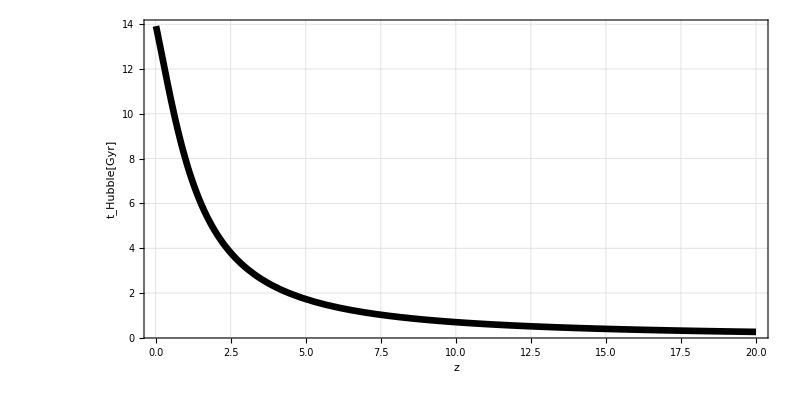

```mathematica
(*Plotting the tHubble as a function of redshift*)
Plot[tHubble[z],{z,0.01,20},GridLines->Automatic,Frame->True,PlotRange->All,FrameLabel->{"z","t_Hubble[Gyr]"},LabelStyle->{FontFamily->"Times",FontSize->32},PlotStyle->{Black,Thickness[0.006]},FrameStyle->Directive[Black,Thick],ImageSize->{800,400},GridLines->All,AspectRatio->.5]
```

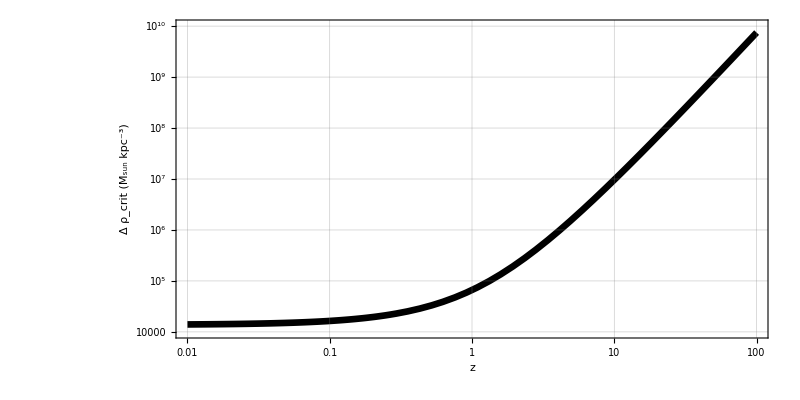

```mathematica
(*Plotting the critical density as a function of redshift*)
LogLogPlot[Deltaoverdensity[z]*rhocrit[z],{z,0.01,100},GridLines->Automatic,Frame->True,PlotRange->{{10^-2,100},{10^4,10^10}},FrameLabel->{"z","Δ ρ_crit (M_sun kpc^-3)"},LabelStyle->{FontFamily->"Times",FontSize->32},PlotStyle->{Black,Thickness[0.006]},FrameStyle->Directive[Black,Thick],ImageSize->{800,400},GridLines->All,AspectRatio->.5]
```

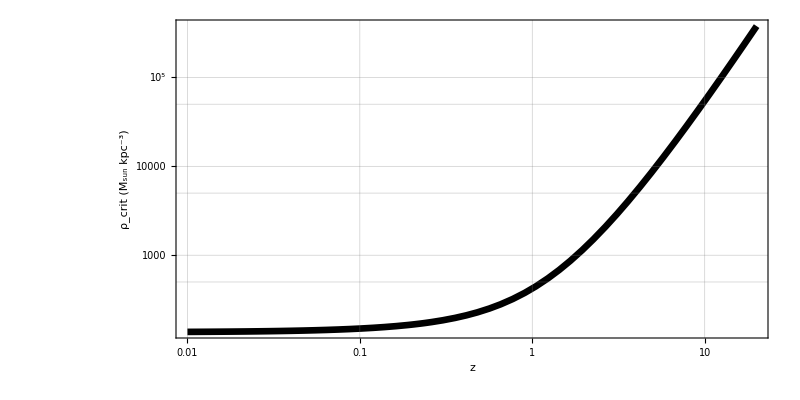

```mathematica
LogLogPlot[rhocrit[z],{z,0.01,20},GridLines->Automatic,Frame->True,PlotRange->All,FrameLabel->{"z","ρ_crit (M_sun kpc^-3)"},LabelStyle->{FontFamily->"Times",FontSize->32},PlotStyle->{Black,Thickness[0.006]},FrameStyle->Directive[Black,Thick],ImageSize->{800,400},GridLines->All,AspectRatio->.5]
```

### NFW Parameter Values/Functions

```mathematica
rhoNFW[r_,rs_,rho0_]:= rho0/((r/rs)(1+r/rs)^2)
rho0NFW[concentration_,z_]:= 1/3 concentration^3/gfunc[concentration] Deltaoverdensity[z]*rhocrit[z] (*Msun/kpc^3*)
massenclosedNFW[r_,rs_,concentration_,z_]:= 4π rho0NFW[concentration,z]*rs^3*gfunc[r/rs] (*Msun, remember to put r, rs in kpc*)
rvirNFW[Mvir_,z_]:= ((3Mvir)/(4π Deltaoverdensity[z]*rhocrit[z]))^(1/3)(*kpc, remember to put Mvir in Msun*)
```

### ADM Atomic Cooling Functions and Analysis

```mathematica
(*Collisional Ionisation*)
Pcolliongizmo[T_]:=1*^-11 2.18 5.85*^-11 T^(1/2)/(1+(T/10^5)^(1/2))Exp[-157809.1/T]
Rcolliongizmo[T_]:= 5.85*^-11 T^(1/2)/(1+(T/10^5)^(1/2))Exp[-157809.1/T]
RcollionHe0gizmo[T_]:= 2.38*^-11 * T^(1/2)*1/(1+(T/10^5)^(1/2))*Exp[-285335.4/T]
PcollionHe0gizmo[T_]:= 3.94*^-11 * RcollionHe0gizmo[T]
RcollionHeIgizmo[T_]:=5.68*^-12 * T^(1/2)*1/(1+(T/10^5)^(1/2))*Exp[-631515.0/T]
PcollionHeIgizmo[T_]:= 8.72*^-11 * RcollionHeIgizmo[T]
Rcollionadm[mc_,a_,T_]:= 1/((a/α)(mc/me)^2)* Rcolliongizmo[T/((mc/me)*(a/α)^2)]
Pcollionadm[mc_,a_,T_]:=(a/α)/(mc/me)*Pcolliongizmo[T/((mc/me)*(a/α)^2)]
(*Collisional Excitation*)
Pcollexcgizmo[T_]:=7.5*^-19 1/(1+(T/10^5)^(1/2))Exp[-118348/T]
PcollexcHeIgizmo[T_]:= 5.54*^-17 * T^-0.397/(1 + (T/10^5)^(1/2))Exp[-473638/T]
Pcollexcadm[mc_,a_,T_]:= (a/α)/(mc/me)*Pcollexcgizmo[T/((mc/me)*(a/α)^2)]
(*Bremsstrahlung*)
Pffgizmo[T_]:= 1.43*^-27  *T^(1/2)(1.1+0.34 Exp[-(5.5-Log10[T])^2/3])
gff = 1.45;
Pffadm[mc_,a_,T_]:=gff*3.7*^-27 (a/0.01)^3 T^(1/2) * ((0.511*10^-3)/mc)^(3/2)
(*Recombination*)
Precgizmo[T_]:=1.036*^-16 *T(7.982*^-11(1.774/T^0.5)(1+T^0.5/1.774)^-0.252(1+T^0.5/838.81)^-1.748)
Rrecgizmo[T_]:= (7.982*^-11(1.774/T^0.5)(1+T^0.5/1.774)^-0.252(1+T^0.5/838.81)^-1.748)
RrecHeIgizmo[T_] := 9.356*^-10 *(0.2065/T^(1/2))*(1+T^0.5/0.2065)^-0.2108*(1+T^0.5/6063.0)^-1.7892
PrecHeIgizmo[T_]  := 1.036*^-16 * T*RrecHeIgizmo[T]
RrecHeIIgizmo[T_]:= 1.5964*^-10 * (2.5092/T^0.5)*(1+T^0.5/2.5092)^-0.252*(1+T^0.5/1677.6)^-1.748
PrecHeIIgizmo[T_] := 1.036*^-16 * T*RrecHeIIgizmo[T]
RrecDigizmo[T_]:= 1.9*^-3 * T^-1.5*Exp[-470000/T]*(1+0.3*Exp[-94000/T])
PrecDigizmo[T_]:= 6.526*^-11 *RrecDigizmo[T]
Precadm[mc_,a_,T_]:= (a/α)^4/(mc/me)*Precgizmo[T/((mc/me)*(a/α)^2)]
Rrecadm[mc_,a_,T_]:= (a/α)^2/(mc/me)^2*Rrecgizmo[T/((mc/me)*(a/α)^2)]
(*Computing number densities with collisional ionisation equilibrium*)
neadm[mc_,a_,T_]:=  Rcollionadm[mc,a,T]/(Rrecadm[mc,a,T]  + Rcollionadm[mc,a,T])//Quiet
nH0adm[mc_,a_,T_]:=  Rrecadm[mc,a,T]/(Rrecadm[mc,a,T]  + Rcollionadm[mc,a,T])//Quiet
(*Total cooling rate function*)
totalCoolRateadm[mc_,a_,T_]:= Module[{xe,xH},
xe = neadm[mc,a,T];
xH = nH0adm[mc,a,T];
(Precadm[mc,a,T]+ Pffadm[mc,a,T])*xe*xe + (Pcollexcadm[mc,a,T]+Pcollionadm[mc,a,T])*xe*xH
];
(*Cooling time function*)
cooltimeatomic[T_,n_,mc_,mX_,a_]:= Module[{coolrate,time},
coolrate = totalCoolRateadm[mc,a,T]*n^2;
time =  (3/2*n*kb*T)/coolrate;
time * secondstoGYr
]
(*virial temperature function*)
Tvirialfunc[Mvir_,Rvir_,mx_]:=N[ 555*10^3*(Mvir/10^12)*(200/Rvir)*(mx/1)]; (*Kelvin, M in Msun, R in kpc, mX in GeV*)
Mvirialfunc[mp_,Tvir_]:= 10^10*(0.93827/mp)^(3/2)*(Tvir/10^4.32)^(3/2) (*Msun*)
```

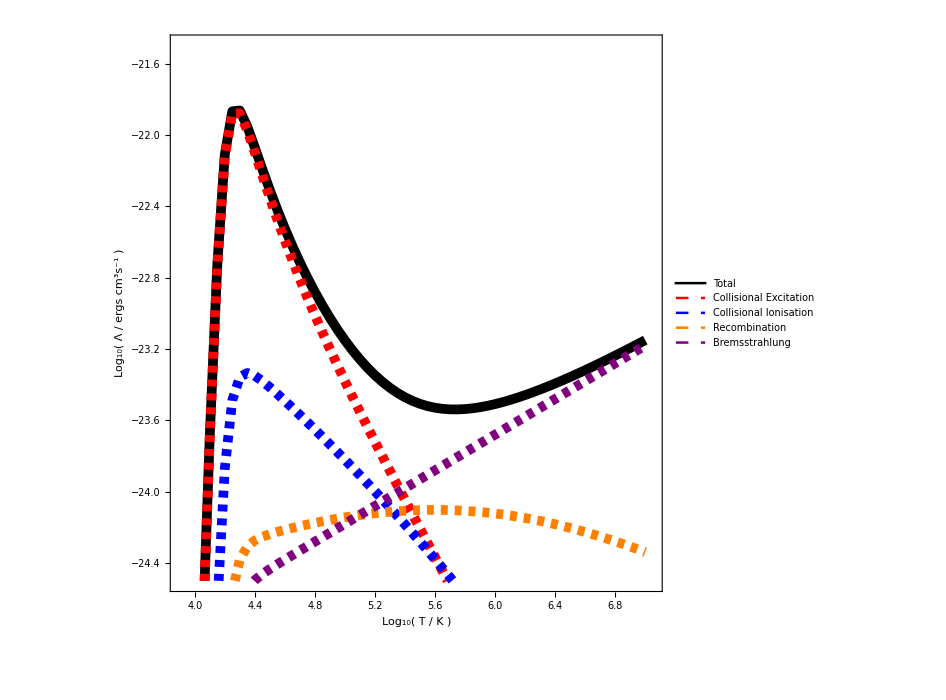

```mathematica
(*Plotting the split up cooling rate*)
MvirTicks = Table[{logT,NumberForm[Log10[Mvirialfunc[mp,10^logT]],{3,1}]},{logT,3,7,0.5}];
mc = me; mx = mp; a = α;
logtmin = 3 + Log10[(a/α)^2 mc/me]; logtmax = 7+ Log10[(a/α)^2 mc/me];dlogt = 0.05;
totalcoollist = Table[{logT,Log10[totalCoolRateadm[mc,a,10^logT]]},{logT,logtmin,logtmax,dlogt}];
collexccoollist = Table[{logT,Log10[Pcollexcadm[mc,a,10^logT]*neadm[mc,a,10^logT]*nH0adm[mc,a,10^logT]]},{logT,logtmin,logtmax,dlogt}];
collioncoollist = Table[{logT,Log10[Pcollionadm[mc,a,10^logT]*neadm[mc,a,10^logT]*nH0adm[mc,a,10^logT]]},{logT,logtmin,logtmax,dlogt}];
recombcoollist = Table[{logT,Log10[Precadm[mc,a,10^logT]*neadm[mc,a,10^logT]^2]},{logT,logtmin,logtmax,dlogt}];
bremcoollist = Table[{logT,Log10[Pffadm[mc,a,10^logT]*neadm[mc,a,10^logT]^2]},{logT,logtmin,logtmax,dlogt}];
legendfontsize = 26; legendspacings = 0.4; linethickness = 0.005;
coolplot = ListLinePlot[{totalcoollist,collexccoollist,collioncoollist,recombcoollist,bremcoollist},Frame->True,FrameLabel->{{"Log_10( Λ / ergs cm^3s^-1 )",""},{"Log_10( T / K )","Log_10( M_vir/M_⊙ )"}},FrameTicks->{{Automatic,Automatic},{Automatic,MvirTicks}},PlotLegends->Placed[LineLegend[{Style["Total",legendfontsize],Style["Collisional Excitation",legendfontsize],Style["Collisional Ionisation",legendfontsize],Style["Recombination",legendfontsize],Style["Bremsstrahlung",legendfontsize]},Spacings->{legendspacings,legendspacings,legendspacings}],{0.71,0.78}],PlotStyle->{{Black,Thickness[0.01]},{Red,Thickness[0.01],Dashed},{Blue,Thickness[0.01],Dashed},{Orange,Thickness[0.01],Dashed},{Purple,Thickness[0.01],Dashed}},ImageSize->{700,700},AspectRatio->1.0,LabelStyle->{FontFamily->"Times",FontSize->32},PlotRange->{{3.9 + Log10[(a/α)^2 mc/me],7.05+ Log10[(a/α)^2 mc/me]},{-24.5,-21.5}},FrameStyle->Directive[Black,Thick]]
```

```mathematica
Tvirialfunc[10^7,Rvir_,mx_] (*Kelvin, M in Msun, R in kpc, mX in GeV*)
(*Mvir/(4/3 π Rvir^3)=overdensity*rhocrit at z=5*)
```

(1110. mx_)/Rvir_

## Evolution of Halo Mass with Redshift

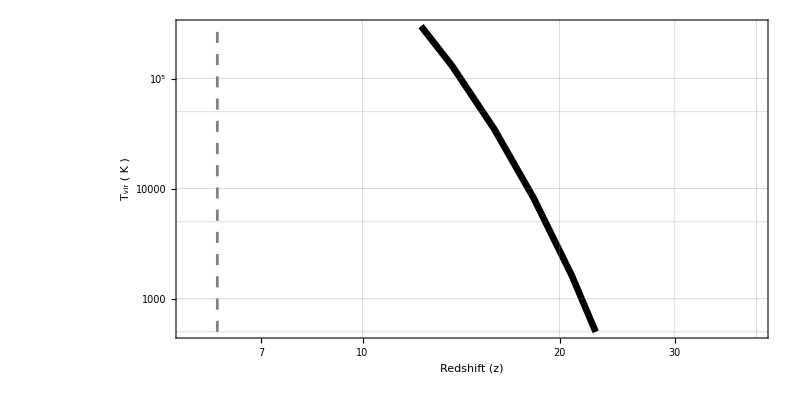

```mathematica
(*Plotting the evolution of the virial temperature as a function of time, pick your favourite mass/parameters!*)

(* Pick redshift at which we want to examine *)
z0 =6;

(* Changed to 10^10,10^11,10^12,10^13 solar mass halo at z=6, the corresponding f(Subscript[M, 0]) are, according to 1409.5228, 0.6, 0.7, 0.8, 1.0 respectively *)

Mhostvsredshift[z_]:= 10^13*Exp[-1.0*(z-z0)] 

(*heuristic function derived from m10q simulations, feel free to add your own favourite params here :)*)

Rhostvsredshift[z_]:= rvirNFW[Mhostvsredshift[z],z]
Tvirialhostvsredshift[z_]:=Tvirialfunc[Mhostvsredshift[z],Rhostvsredshift[z],mp]
LogLogPlot[Tvirialhostvsredshift[z],{z,0,100},GridLines->Automatic,Frame->True,PlotRange->{{0.9*z0,40},{5*10^2,3*10^5}},FrameLabel->{"Redshift (z)","T_vir ( K )"},LabelStyle->{FontFamily->"Times",FontSize->32},PlotStyle->{Black,Thickness[0.006]},FrameStyle->Directive[Black,Thick],ImageSize->{800,400},GridLines->All,AspectRatio->.5,Epilog->{Directive[Gray,Thickness[0.0025],Dashing[{0.01,0.01}]],Line[{{Log[z0],Log[5*10^2]},{Log[z0],Log[3*10^5]}}]}]
```

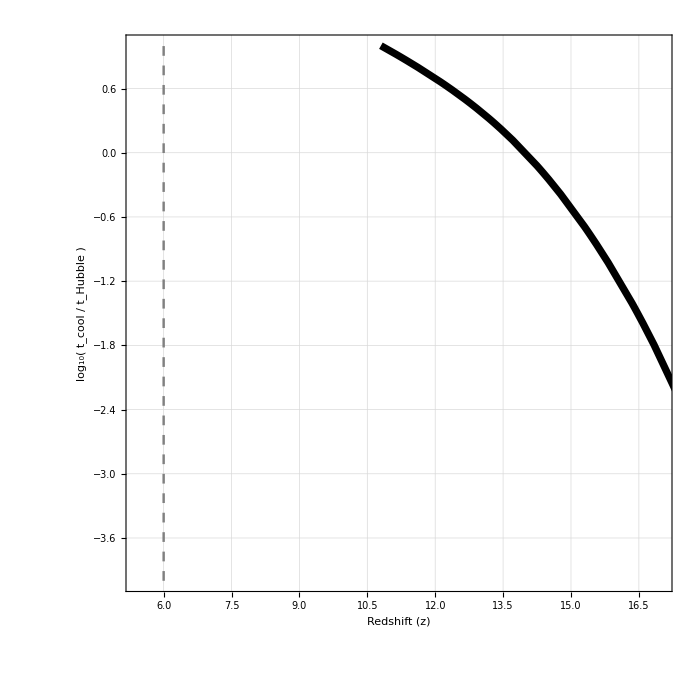

```mathematica
linethickness = 0.0075;
Plot[{Log10[cooltimeatomic[Tvirialhostvsredshift[z], (0.05*Deltaoverdensity[z]*rhocrit[z]/(kpctocm^3))/(mp*GeVtoMsun),3me,mp,Sqrt[0.5/3]α]/tHubble[z]]},{z,0,100},GridLines->Automatic,Frame->True,
PlotRange->{{0.9*z0,17},{-4,1}},FrameLabel->{"Redshift (z)","log_10( t_cool / t_Hubble )"},LabelStyle->{FontFamily->"Times",FontSize->32},PlotStyle->{{Black,Thickness[linethickness]}},FrameStyle->Directive[Black,Thick],ImageSize->{700,700},GridLines->All,AspectRatio->1,Epilog->{Directive[Gray,Thickness[0.0025],Dashing[{0.01,0.01}]],Line[{{z0,-4},{z0,1}}]}]
```

```mathematica
(*Integral of 1/(Subscript[t, cool](z)) over dz*)
(*Define the derivative of thubble[z] w.r.t.z*)dtHubbledz[z_?NumericQ]:=Derivative[1][tHubble][z]
(*Define the integral function*)
(*Define the integrand as a function*)integrand[z_?NumericQ,meprime_,mpprime_,alphaprime_,fprime_]:=1/cooltimeatomic[mpprime/mp Tvirialhostvsredshift[z], (fprime*Deltaoverdensity[z]*rhocrit[z]/(kpctocm^3))/(mpprime*GeVtoMsun),meprime,mpprime,alphaprime]*dtHubbledz[z]

(*Numerically integrate the integrand over a specific range of z*)(*Here,as an example,we integrate from z1 to z2,where you should define these limits*)integralValueNumerical[z_?NumericQ,meprime_,mpprime_,alphaprime_,fprime_]:=NIntegrate[integrand[zp,meprime,mpprime,alphaprime,fprime],{zp,30.0,z},MaxRecursion->30]

(*adm1pt5metageovertcool = Table[{z,integralValueNumerical[z,1.5me,mp,Sqrt[0.5/1.5]α,0.05]},{z,0.01,20,0.5}];*)
adm1pt5metageovertcool = Table[{z,integralValueNumerical[z,0.039,1.03,0.0058,0.15]},{z,z0,20,0.5}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{6.,0.81119},{6.5,0.810591},{7.,0.809619},{7.5,0.807941},{8.,0.804845},{8.5,0.798732},{9.,0.785714},{9.5,0.755499},{10.,0.677953},{10.5,0.461283},{11.,0.0653263},{11.5,0.000165219},{12.,2.36218×10^-8},{12.5,1.63198×10^-13},{13.,1.90114×10^-20},{13.5,8.74163×10^-30},{14.,2.20224×10^-42},{14.5,2.06836×10^-59},{15.,1.86336×10^-82},{15.5,1.09874×10^-113},{16.,4.72605×10^-156},{16.5,1.39081×10^-213},{17.,0.},{17.5,0.},{18.,0.},{18.5,0.},{19.,0.},{19.5,0.},{20.,0.}}

```mathematica
1/0.81119
```

1.23276

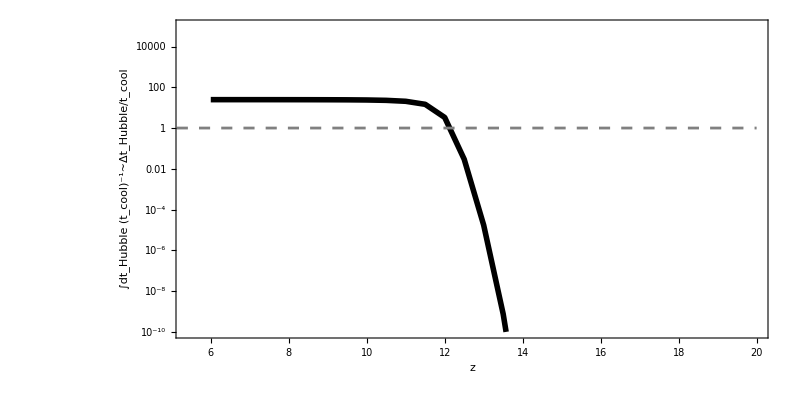

```mathematica
linethickness = 0.005;
(*Plot the integral function*)
ListLogPlot[{adm1pt5metageovertcool},GridLines->Automatic,Joined->True,Frame->True,PlotRange->{{0.9*z0,20.0},{10^-10,1*10^5}},FrameLabel->{"z","∫dt_Hubble (t_cool)^-1~Δt_Hubble/t_cool"},LabelStyle->{FontFamily->"Times",FontSize->28},PlotStyle->{{Black,Thickness[linethickness]}},FrameStyle->Directive[Black,Thick],ImageSize->{800,400},GridLines->All,AspectRatio->.5,Epilog->{Directive[Gray,Thickness[0.0025],Dashing[{0.01,0.01}]],Line[{{0,Log[1]},{20,Log[1]}}],Text["",{18,Log[1]},{1,0}]}]
```

Below is a contour plot of the integrated quantity above for different ADM parameter points. It’s quite slow to run (you can speed up by reducing the PlotPoints option at the expense of making the grid coarser). One can make similar plots for any halo mass and redshift of interest (you would need to change the final redshift of the integral).

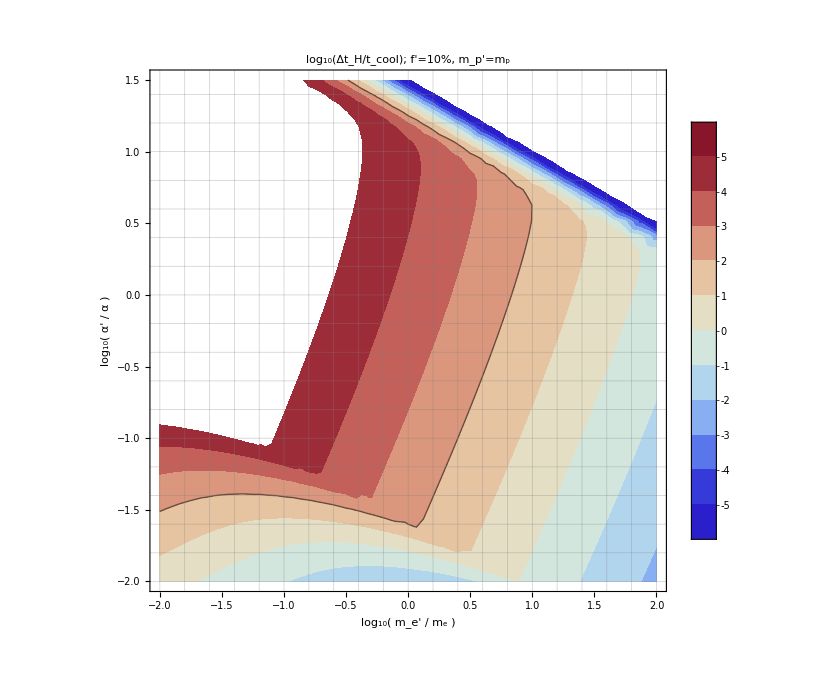

```mathematica
xmin = -2;xmax = 2;
ymin = -2;  ymax = 1.5;
logtcoolmin = -5; logtcoolmax = 5;
customThermometerColors[z_]:=If[z<logtcoolmin,ColorData["ThermometerColors"][-1],If[z>logtcoolmax,ColorData["ThermometerColors"][1],ColorData["ThermometerColors"][Rescale[z,{logtcoolmin,logtcoolmax}]]]]

contourplot = ContourPlot[Log10[integralValueNumerical[z0,(10^logrme)me,mp,(10^logra)α,0.1]],{logrme,xmin,xmax},{logra,ymin,ymax},PlotLegends->Automatic,PlotLabel->StringForm["log_10(Δt_H/t_cool); f'=10%, m_p'=m_p",Round[0.05*100],Round[mp/mp,0.1]],PlotPoints->3,Frame->True,FrameLabel->{"log_10( m_e' / m_e )","log_10( α' / α )"},Contours->Range[logtcoolmin,logtcoolmax,1],ColorFunction->customThermometerColors,ColorFunctionScaling->False,ContourStyle->Table[If[i==2,{Thick,Black},None],{i,logtcoolmin,logtcoolmax}],AspectRatio->1.0,LabelStyle->{FontFamily->"Times",FontSize->32},FrameStyle->Directive[Black,Thick],ImageSize->{700,700},GridLines->All,ColorFunction->"Rainbow",RegionFunction->Function[{x,y,z},z<=logtcoolmax]]//Quiet;
(*points = Graphics[{
{Black,PointSize[0.02],Point[
{Log10[3],Log10[Sqrt[0.5/3]]}]}
}];*)
(*Show[contourplot,points]*)
Show[contourplot]
```

```mathematica
Export["/Users/linda/Dropbox/lyman_alpha/plots/f=0.1_mp'=mp/z_4_10_13_halo_mass_f_0.1_mp.pdf",contourplot]
```

/Users/linda/Dropbox/lyman_alpha/plots/f=0.1_mp'=mp/z_4_10_13_halo_mass_f_0.1_mp.pdf

```mathematica
xmin = -2;xmax = 2;
ymin = -1.;  ymax = 2.5;
logtcoolmin = -5; logtcoolmax = 5;
f1=0.01;
f2=0.03;
f3=0.05;
f4=0.07;
f5=0.1;
f6=0.3;
f7=1.;
mpprime =1000mp;
customThermometerColors[z_]:=If[z<logtcoolmin,ColorData["ThermometerColors"][-1],If[z>logtcoolmax,ColorData["ThermometerColors"][1],ColorData["ThermometerColors"][Rescale[z,{logtcoolmin,logtcoolmax}]]]]

contourplot1 = ContourPlot[Log10[integralValueNumerical[z0,(10^logrme)me,mpprime,(10^logra)α,f1]],{logrme,xmin,xmax},{logra,ymin,ymax},PlotLegends->Automatic,PlotLabel->StringForm["log_10(Δt_H/t_cool); m_p'=1000m_p",Round[0.05*100],Round[mp/mp,0.1]],PlotPoints->3,Frame->True,FrameLabel->{"log_10( m_e' / m_e )","log_10( α' / α )"},Contours->{2},ContourShading->None,
ContourStyle->{Thick,Black},AspectRatio->1.0,
ContourLabels->(Text[Style["f=0.01",FontSize->22,FontFamily->"Times"],{-0.8,-0.8},Background->White]&),LabelStyle->{FontFamily->"Times",FontSize->32},FrameStyle->Directive[Black,Thick],ImageSize->{700,700},GridLines->All,RegionFunction->Function[{x,y,z},z<=logtcoolmax]]//Quiet;
contourplot2 = ContourPlot[Log10[integralValueNumerical[z0,(10^logrme)me,mpprime,(10^logra)α,f2]],{logrme,xmin,xmax},{logra,ymin,ymax},PlotLegends->Automatic,Contours->{2},ContourShading->None,
ContourStyle->{Thick,Black},AspectRatio->1.0,
ContourLabels->(Text[Style[f2,FontSize->22,FontFamily->"Times"],{-0.8,-1.3},Background->White]&),LabelStyle->{FontFamily->"Times",FontSize->32},FrameStyle->Directive[Black,Thick],ImageSize->{700,700},GridLines->All,RegionFunction->Function[{x,y,z},z<=logtcoolmax]]//Quiet;
contourplot3 = ContourPlot[Log10[integralValueNumerical[z0,(10^logrme)me,mpprime,(10^logra)α,f3]],{logrme,xmin,xmax},{logra,ymin,ymax},PlotLegends->Automatic,Contours->{2},ContourShading->None,
ContourStyle->{Thick,Black},AspectRatio->1.0,
ContourLabels->(Text[Style[f3,FontSize->22,FontFamily->"Times"],{-0.4,-1.2},Background->White]&),LabelStyle->{FontFamily->"Times",FontSize->32},FrameStyle->Directive[Black,Thick],ImageSize->{700,700},GridLines->All,RegionFunction->Function[{x,y,z},z<=logtcoolmax]]//Quiet;
contourplot5 = ContourPlot[Log10[integralValueNumerical[z0,(10^logrme)me,mpprime,(10^logra)α,f5]],{logrme,xmin,xmax},{logra,ymin,ymax},PlotLegends->Automatic,Contours->{2},ContourShading->None,
ContourStyle->{Thick,Black},AspectRatio->1.0,
ContourLabels->(Text[Style[f5,FontSize->22,FontFamily->"Times"],{0.4,-0.6},Background->White]&),
LabelStyle->{FontFamily->"Times",FontSize->32},FrameStyle->Directive[Black,Thick],ImageSize->{700,700},GridLines->All,RegionFunction->Function[{x,y,z},z<=logtcoolmax]]//Quiet;
contourplot6 = ContourPlot[Log10[integralValueNumerical[z0,(10^logrme)me,mpprime,(10^logra)α,f6]],{logrme,xmin,xmax},{logra,ymin,ymax},PlotLegends->Automatic,Contours->{2},ContourShading->None,
ContourStyle->{Thick,Black},AspectRatio->1.0,
ContourLabels->(Text[Style[f6,FontSize->22,FontFamily->"Times"],{0.5,-0.6},Background->White]&),
LabelStyle->{FontFamily->"Times",FontSize->32},FrameStyle->Directive[Black,Thick],ImageSize->{700,700},GridLines->All,RegionFunction->Function[{x,y,z},z<=logtcoolmax]]//Quiet;
contourplot7 = ContourPlot[Log10[integralValueNumerical[z0,(10^logrme)me,mpprime,(10^logra)α,f7]],{logrme,xmin,xmax},{logra,ymin,ymax},PlotLegends->Automatic,Contours->{2},ContourShading->None,
ContourStyle->{Thick,Black},AspectRatio->1.0,
ContourLabels->(Text[Style[f7,FontSize->22,FontFamily->"Times"],{0.55,-0.6},Background->White]&),
LabelStyle->{FontFamily->"Times",FontSize->32},FrameStyle->Directive[Black,Thick],ImageSize->{700,700},GridLines->All,RegionFunction->Function[{x,y,z},z<=logtcoolmax]]//Quiet;
```

```mathematica
Show[contourplot1,contourplot2,contourplot3,contourplot5,contourplot6,contourplot7]
```

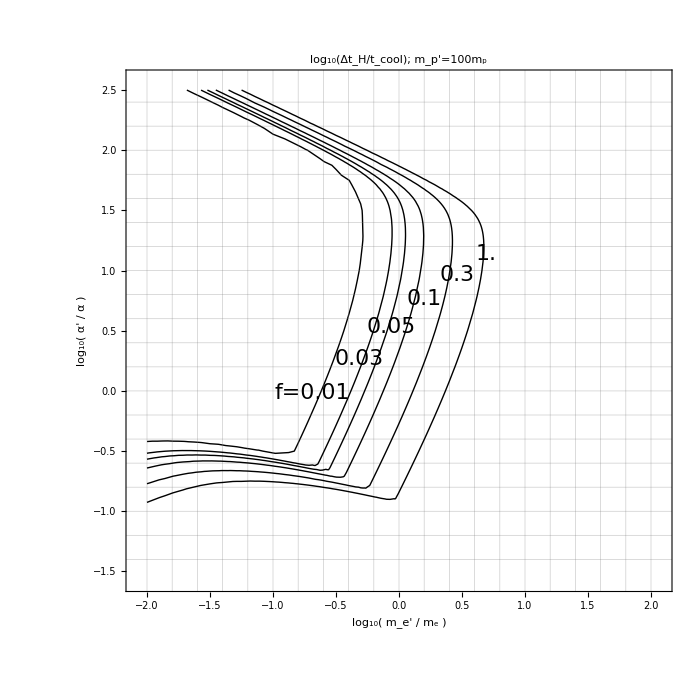

```mathematica
integralValueNumerical[z0,(10^-2)me,10,0.073,0.1]
```

2.46767×10^7

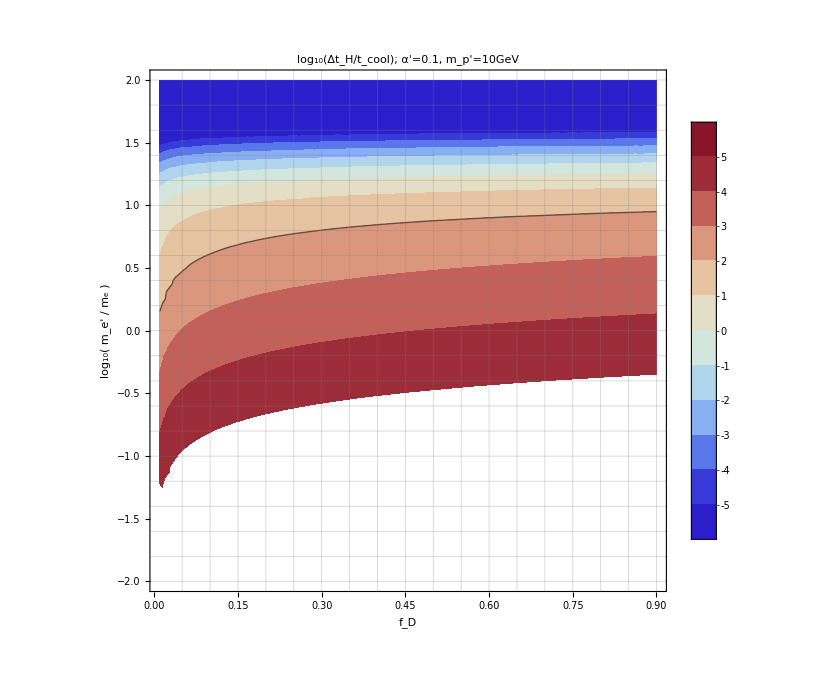

```mathematica
ymin = -2;ymax = 2;
xmin = 0.01;  xmax = 0.9;
logtcoolmin = -5; logtcoolmax = 5;
customThermometerColors[z_]:=If[z<logtcoolmin,ColorData["ThermometerColors"][-1],If[z>logtcoolmax,ColorData["ThermometerColors"][1],ColorData["ThermometerColors"][Rescale[z,{logtcoolmin,logtcoolmax}]]]]

contourplot = ContourPlot[Log10[integralValueNumerical[z0,(10^logrme)me,10,0.1,fD]],{fD,xmin,xmax},{logrme,ymin,ymax},PlotLegends->Automatic,PlotLabel->StringForm["log_10(Δt_H/t_cool); α'=0.1, m_p'=10GeV",Round[0.05*100],Round[mp/mp,0.1]],PlotPoints->3,Frame->True,FrameLabel->{"f_D","log_10( m_e' / m_e )"},Contours->Range[logtcoolmin,logtcoolmax,1],ColorFunction->customThermometerColors,ColorFunctionScaling->False,ContourStyle->Table[If[i==2,{Thick,Black},None],{i,logtcoolmin,logtcoolmax}],AspectRatio->1.0,LabelStyle->{FontFamily->"Times",FontSize->32},FrameStyle->Directive[Black,Thick],ImageSize->{700,700},GridLines->All,ColorFunction->"Rainbow",RegionFunction->Function[{x,y,z},z<=logtcoolmax]]//Quiet;
(*points = Graphics[{
{Black,PointSize[0.02],Point[
{Log10[3],Log10[Sqrt[0.5/3]]}]}
}];*)
(*Show[contourplot,points]*)
Show[contourplot]
```

```mathematica
(*make grid of params and make cooling data*)
```

```mathematica
logmeD = Table[x,{x,-4,-1,0.1}];
logmpD = Table[x,{x,0,3,0.1}];
alphaD = Table[x,{x,0.005,0.2,0.005}];
```

```mathematica
coolingdata=Table[{logmeD[[j1]],logmpD[[j2]],alphaD[[j3]],Log10[integralValueNumerical[z0,10^logmeD[[j1]],10^logmpD[[j2]],alphaD[[j3]],0.3]]},{j1,1,Length[logmeD]},{j2,1,Length[logmpD]},{j3,1,Length[alphaD]}];
```

```mathematica
data=Flatten[coolingdata,2]
```

{{-4.,0.,0.005,5.45894},{-4.,0.,0.01,5.69855},{-4.,0.,0.015,5.82589},{-4.,0.,0.02,5.90914},38432,{-1.,3.,0.185,-3.29113},{-1.,3.,0.19,-3.3706},{-1.,3.,0.195,-3.45782},{-1.,3.,0.2,-3.55258}}
 |  |  |  |

```mathematica
Export["/Users/linda/Dropbox/lyman_alpha/linda/f0.3_coolingdata.txt",data,"Table", "FieldSeparators"->" "]
```

/Users/linda/Dropbox/lyman_alpha/linda/f0.3_coolingdata.txt

```mathematica
(*make cooling data for some grid of adm params*)
```

```mathematica
cmbdata=ToExpression[Import["/Users/linda/Dropbox/lyman_alpha/linda/for_math_full_f0.05_xi0.2.txt","List"]][[1]];
```

```mathematica
Length[cmbdata]
```

4422

```mathematica
coolingdata=Table[{cmbdata[[i,1]],cmbdata[[i,2]],cmbdata[[i,3]],Log10[integralValueNumerical[z0,10^cmbdata[[i,2]],10^cmbdata[[i,1]],cmbdata[[i,3]],0.01]]},{i,1,Length[cmbdata]}];
```

```mathematica
coolingdata=DeleteCases[coolingdata,a_/;a[[-1]]>2]
```

{{2.0588,-3.74218,0.0180131,1.88939},3487,{2.6393,-2.83122,0.0893272,-0.171607}}
 |  |  |  |

```mathematica
Export["/Users/linda/Dropbox/lyman_alpha/linda/f0.05_xi0.2_full_cmbcoolingdata.txt",coolingdata,"Table", "FieldSeparators"->" "]
```

/Users/linda/Dropbox/lyman_alpha/linda/f0.05_xi0.2_full_cmbcoolingdata.txt

```mathematica
1/2*0.01^2*0.0055 GeV/Kelvin
```

3.18841×10^6

```mathematica
1/2 α^2 me
```

1.36129×10^-8